### What does boost - Invaraince mean?

```mathematica
Ωd[d_]:=(2 π^(d/2))/Gamma[d/2]
```

```mathematica
FullSimplify[Integrate[l^(d-1)/((l^2+Δ)^2),{l,0,Infinity}] Ωd[d]/(2π)^d-Gamma[2-d/2]/(Gamma[2] (4 π)^(d/2)) Δ^(-2+d/2)]
```

ConditionalExpression[0,d<4&&(Re[Δ]≥0||Δ∉Reals)&&d Arg[1/Δ]≤2 π&&d>0]

```mathematica
FullSimplify[Integrate[FullSimplify[k/(k^2+μ^2)(Gamma[2-d/2]/(Gamma[2] (4 π)^(d/2)) Δ^(-2+d/2)/.{Δ-> x(1-x) k^2+μ^2,d->2}),k>0]/(2π),{k,0,Infinity}],μ>0&&x<1&&x>0]
```

-Log[-(-1+x) x]/(16 π^2 (1+(-1+x) x) μ^2)

```mathematica
FullSimplify[Integrate[-Log[-(-1+x) x]/(16 π^2 (1+(-1+x) x) μ^2),{x,0,1}]]
```

(PolyGamma[1,1/6]+PolyGamma[1,1/3]-PolyGamma[1,2/3]-PolyGamma[1,5/6])/(288 π^2 μ^2)

```mathematica
y[θ_]=Log[TrigFactor[1/Tan[θ]+1/Sin[θ]]]
```

Log[Cot[θ/2]]

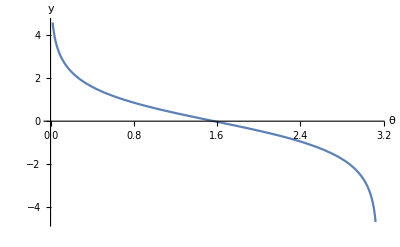

```mathematica
Plot[y[θ],{θ,0,π},AxesLabel->{θ,y}]
```

```mathematica
boostInv[θ_]=-TrigFactor[D[y[θ],θ]]
```

1/2 Csc[θ/2] Sec[θ/2]

```mathematica
y[π/2]
boostInv[π/2]
```

0

1

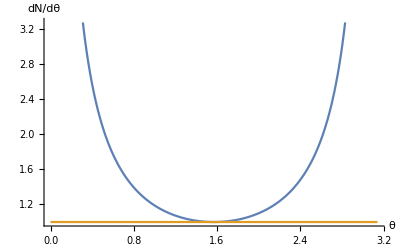

```mathematica
Plot[{boostInv[θ],boostInv[π/2]},{θ,0,π},AxesLabel->{θ,dN/dθ}]
```

```mathematica
FullSimplify[Solve[(Sqrt[1-cθ^2]+cθ)/(Sqrt[1-cθ^2] cθ)==Exp[y],cθ]]
```

{{cθ→1/2 (ⅇ^-y+√(1+ⅇ^(-2 y))-√(1-2 ⅇ^(-2 y) (1+ⅇ^y √(1+ⅇ^(-2 y)))))},{cθ→1/2 (ⅇ^-y+√(1+ⅇ^(-2 y))+√(1-2 ⅇ^(-2 y) (1+ⅇ^y √(1+ⅇ^(-2 y)))))},{cθ→1/2 ⅇ^-y (1-ⅇ^y (√(1+ⅇ^(-2 y))+√(1+2 ⅇ^(-2 y) (-1+ⅇ^y √(1+ⅇ^(-2 y))))))},{cθ→1/2 (ⅇ^-y-√(1+ⅇ^(-2 y))+√(1+2 ⅇ^(-2 y) (-1+ⅇ^y √(1+ⅇ^(-2 y)))))}}

```mathematica
soltz=FullSimplify[Solve[{τ==Sqrt[t^2-z^2],η==1/2 Log[(t+z)/(t-z)]},{t,z}]]
```

{{t→-τ Cosh[η],z→-τ Sinh[η]},{t→τ Cosh[η],z→τ Sinh[η]}}

```mathematica
solvz=FullSimplify[Solve[{1==Sqrt[vT^2+vz^2],yp==1/2 Log[(1+vz)/(1-vz)]},{vT,vz}],-π<2 Im[y]≤π]
```

{{vT→-Sech[yp],vz→Tanh[yp]},{vT→Sech[yp],vz→Tanh[yp]}}

```mathematica
δz=FullSimplify[(z-t vz)/.soltz[[2]]/.solvz[[2]]]
```

τ (Sinh[η]-Cosh[η] Tanh[yp])

```mathematica
FullSimplify[Solve[δz==0,η],yp∈Reals&&η∈Reals]
```

{{η→ConditionalExpression[yp+ⅈ π (1+2 C[1]),C[1]∈Integers]},{η→ConditionalExpression[yp+2 ⅈ π C[1],C[1]∈Integers]}}

### G12

```mathematica
n1:=n3cl+n4cl+3(n3qu+n4qu)+1
n2:=2 n3cl+3 n4cl+n4qu+1-4
```

```mathematica
n22=FullSimplify[(n2-n1)/2]
```

1/2 (-4+n3cl+2 n4cl+n4qu-3 (n3qu+n4qu))

```mathematica
n3:=n3cl+n3qu
n4:=n4cl+n4qu
```

```mathematica
soln3cl=FullSimplify[Solve[n3+2n4==6,n3cl]]
```

{{n3cl→-n3qu-2 (-3+n4cl+n4qu)}}

```mathematica
FullSimplify[n22/.soln3cl[[1]]]
```

1-2 n3qu-2 n4qu

### G11

```mathematica
n1:=n3cl+n4cl+3(n3qu+n4qu)+2
n2:=2 n3cl+3 n4cl+n4qu-4
```

```mathematica
n22=FullSimplify[(n2-n1)/2]
```

1/2 (-6+n3cl+2 n4cl+n4qu-3 (n3qu+n4qu))

```mathematica
n3:=n3cl+n3qu
n4:=n4cl+n4qu
```

```mathematica
soln3cl=FullSimplify[Solve[n3+2n4==6,n3cl]]
```

{{n3cl→-n3qu-2 (-3+n4cl+n4qu)}}

```mathematica
FullSimplify[n22/.soln3cl[[1]]]
```

-2 (n3qu+n4qu)

## T^μν: use the prescription 1/(kp+i ϵ)

```mathematica
Exit
```

```mathematica
ηu={0,1,0,0}
```

{0,1,0,0}

```mathematica
guu={{0,1,0,0},{1,0,0,0},{0,0,-1,0},{0,0,0,-1}}
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
Proj[ku_,μ_,ν_]:=guu[[μ,ν]]-(ηu[[μ]] ku[[ν]]+ ηu[[ν]] ku[[μ]])/(ηu.guu.ku)
```

```mathematica
k1:={k1p,k1m,k1x,k1y}
l1:={l1p,l1m,l1x,l1y}
```

```mathematica
δT:=DiagonalMatrix[{0,0,1,1}](*for scalar prodcution of transverse components*)
```

```mathematica
GRuu[ku_,μ_,ν_]:=-I/(ku.guu.ku)Proj[ku,μ,ν]
```

```mathematica
Table[GRuu[k1,μ,ν],{μ,1,4},{ν,1,4}]
```

{{0,0,0,0},{0,(2 ⅈ k1m)/(k1p (2 k1m k1p-k1x^2-k1y^2)),(ⅈ k1x)/(k1p (2 k1m k1p-k1x^2-k1y^2)),(ⅈ k1y)/(k1p (2 k1m k1p-k1x^2-k1y^2))},{0,(ⅈ k1x)/(k1p (2 k1m k1p-k1x^2-k1y^2)),ⅈ/(2 k1m k1p-k1x^2-k1y^2),0},{0,(ⅈ k1y)/(k1p (2 k1m k1p-k1x^2-k1y^2)),0,ⅈ/(2 k1m k1p-k1x^2-k1y^2)}}

```mathematica
Acl[μ_,ku_,lu_]:=(I/ku[[2]] GRuu[ku,μ,2]+2/((ku-lu).δT.(ku-lu)) 1/(ku.guu.ku)(-(guu.δT.(ku-lu))[[μ]]+ηu[[μ]] ku.δT.(ku-lu)/ku[[1]]))
```

```mathematica
Acl[ku_,lu_]:=Table[Acl[i,ku,lu],{i,1,4}]
```

```mathematica
Acl[k1,l1]
```

{0,-2/(k1p (2 k1m k1p-k1x^2-k1y^2))+(2 (k1x (k1x-l1x)+k1y (k1y-l1y)))/(k1p (2 k1m k1p-k1x^2-k1y^2) ((k1x-l1x)^2+(k1y-l1y)^2)),-k1x/(k1m k1p (2 k1m k1p-k1x^2-k1y^2))+(2 (k1x-l1x))/((2 k1m k1p-k1x^2-k1y^2) ((k1x-l1x)^2+(k1y-l1y)^2)),-k1y/(k1m k1p (2 k1m k1p-k1x^2-k1y^2))+(2 (k1y-l1y))/((2 k1m k1p-k1x^2-k1y^2) ((k1x-l1x)^2+(k1y-l1y)^2))}

```mathematica
DAuu[ku_,μ_,lu_,ν_]:=-I ku[[μ]] Acl[ν,ku,lu]
```

```mathematica
DAuu[ku_,lu_]:=Table[DAuu[ku,μ,lu,ν],{μ,1,4},{ν,1,4}]
```

```mathematica
muu=Limit[FullSimplify[ k1m DAuu[k1,l1]],k1m->0]
```

{{0,0,-(ⅈ k1x)/(k1x^2+k1y^2),-(ⅈ k1y)/(k1x^2+k1y^2)},{0,0,0,0},{0,0,-(ⅈ k1x^2)/(k1p (k1x^2+k1y^2)),-(ⅈ k1x k1y)/(k1p (k1x^2+k1y^2))},{0,0,-(ⅈ k1x k1y)/(k1p (k1x^2+k1y^2)),-(ⅈ k1y^2)/(k1p (k1x^2+k1y^2))}}

```mathematica
muu-Transpose[muu]
```

{{0,0,-(ⅈ k1x)/(k1x^2+k1y^2),-(ⅈ k1y)/(k1x^2+k1y^2)},{0,0,0,0},{(ⅈ k1x)/(k1x^2+k1y^2),0,0,0},{(ⅈ k1y)/(k1x^2+k1y^2),0,0,0}}

Therefore, we don' t need this piece, which only gives contributions along the lightcones!

```mathematica
da=FullSimplify[FullSimplify[-I FullSimplify[FullSimplify[(k1.guu.k1) DAuu[k1,l1]]/(2 (k1p))/.{k1m->  (k1x^2+k1y^2)/(2 (k1p))}]]]
```

{{0,(-k1x l1x+l1x^2+l1y (-k1y+l1y))/(k1p ((k1x-l1x)^2+(k1y-l1y)^2)),k1x/(k1x^2+k1y^2)+(-k1x+l1x)/((k1x-l1x)^2+(k1y-l1y)^2),k1y/(k1x^2+k1y^2)+(-k1y+l1y)/((k1x-l1x)^2+(k1y-l1y)^2)},{0,-((k1x^2+k1y^2) ((k1x-l1x) l1x+(k1y-l1y) l1y))/(2 k1p^3 ((k1x-l1x)^2+(k1y-l1y)^2)),(k1x+((k1x^2+k1y^2) (-k1x+l1x))/((k1x-l1x)^2+(k1y-l1y)^2))/(2 k1p^2),(-2 k1x k1y l1x+k1x^2 l1y+k1y (l1x^2+l1y (-k1y+l1y)))/(2 k1p^2 ((k1x-l1x)^2+(k1y-l1y)^2))},{0,(k1x (-k1x l1x+l1x^2+l1y (-k1y+l1y)))/(k1p^2 ((k1x-l1x)^2+(k1y-l1y)^2)),(k1x ((2 k1x)/(k1x^2+k1y^2)+(-2 k1x+2 l1x)/((k1x-l1x)^2+(k1y-l1y)^2)))/(2 k1p),((k1x k1y)/(k1x^2+k1y^2)+(k1x (-k1y+l1y))/((k1x-l1x)^2+(k1y-l1y)^2))/k1p},{0,(k1y (-k1x l1x+l1x^2+l1y (-k1y+l1y)))/(k1p^2 ((k1x-l1x)^2+(k1y-l1y)^2)),(k1y ((2 k1x)/(k1x^2+k1y^2)+(-2 k1x+2 l1x)/((k1x-l1x)^2+(k1y-l1y)^2)))/(2 k1p),(k1y (k1y/(k1x^2+k1y^2)+(-k1y+l1y)/((k1x-l1x)^2+(k1y-l1y)^2)))/k1p}}

```mathematica
DA[{k1p_,k1m_,k1x_,k1y_},{l1p_,l1m_,l1x_,l1y_}]=da
```

{{0,(-k1x l1x+l1x^2+l1y (-k1y+l1y))/(k1p ((k1x-l1x)^2+(k1y-l1y)^2)),k1x/(k1x^2+k1y^2)+(-k1x+l1x)/((k1x-l1x)^2+(k1y-l1y)^2),k1y/(k1x^2+k1y^2)+(-k1y+l1y)/((k1x-l1x)^2+(k1y-l1y)^2)},{0,-((k1x^2+k1y^2) ((k1x-l1x) l1x+(k1y-l1y) l1y))/(2 k1p^3 ((k1x-l1x)^2+(k1y-l1y)^2)),(k1x+((k1x^2+k1y^2) (-k1x+l1x))/((k1x-l1x)^2+(k1y-l1y)^2))/(2 k1p^2),(-2 k1x k1y l1x+k1x^2 l1y+k1y (l1x^2+l1y (-k1y+l1y)))/(2 k1p^2 ((k1x-l1x)^2+(k1y-l1y)^2))},{0,(k1x (-k1x l1x+l1x^2+l1y (-k1y+l1y)))/(k1p^2 ((k1x-l1x)^2+(k1y-l1y)^2)),(k1x ((2 k1x)/(k1x^2+k1y^2)+(-2 k1x+2 l1x)/((k1x-l1x)^2+(k1y-l1y)^2)))/(2 k1p),((k1x k1y)/(k1x^2+k1y^2)+(k1x (-k1y+l1y))/((k1x-l1x)^2+(k1y-l1y)^2))/k1p},{0,(k1y (-k1x l1x+l1x^2+l1y (-k1y+l1y)))/(k1p^2 ((k1x-l1x)^2+(k1y-l1y)^2)),(k1y ((2 k1x)/(k1x^2+k1y^2)+(-2 k1x+2 l1x)/((k1x-l1x)^2+(k1y-l1y)^2)))/(2 k1p),(k1y (k1y/(k1x^2+k1y^2)+(-k1y+l1y)/((k1x-l1x)^2+(k1y-l1y)^2)))/k1p}}

```mathematica
k2:={k2p,k2m,k2x,k2y}
l2:={l2p,l2m,l2x,l2y}
```

```mathematica
Fuu[ku_,lu_]:=Module[{dA},
dA=DA[ku,lu];
FullSimplify[dA-Transpose[dA]]
]
```

```mathematica
Tuu[k1u_,l1u_,k2u_,l2u_]:=Module[{f1uu,f2uu},
f1uu=Fuu[k1u,l1u];f2uu=(Fuu[k2u,l2u]/.{k2u[[3]]->-k1u[[3]],k2u[[4]]->-k1u[[4]],l2u[[3]]->-l1u[[3]],l2u[[4]]->-l1u[[4]]});
FullSimplify[f1uu.guu.f2uu+Tr[Transpose[f1uu].guu.f2uu.guu] guu/4]
]
```

```mathematica
Tμν=Tuu[k1,l1,k2,l2]/(l1.δT.l1)^2
```

{{-1/((k1x^2+k1y^2) ((k1x-l1x)^2+(k1y-l1y)^2) (l1x^2+l1y^2)),(2 k1p k2p ((k1x-l1x)^2+(k1y-l1y)^2) (l1x^2+l1y^2)+k1p^2 ((k1x+k1y-l1x) l1x+(-k1x+k1y) l1y-l1y^2) (-l1x (k1y+l1x)+k1y l1y-l1y^2+k1x (l1x+l1y))-k2p^2 ((k1x+k1y-l1x) l1x+(-k1x+k1y) l1y-l1y^2) (-l1x (k1y+l1x)+k1y l1y-l1y^2+k1x (l1x+l1y)))/(4 k1p^2 k2p^2 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2),(k1p (k1y l1x-k1x l1y) (2 k1x k1y l1x-k1x^2 l1y+k1y (-l1x^2+(k1y-l1y) l1y))-k2p ((k1x-l1x) l1x+(k1y-l1y) l1y) (k1x^2 l1x-k1y^2 l1x-k1x (l1x^2-2 k1y l1y+l1y^2)))/(k1p (k1x^2+k1y^2) k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2),(k1p (k1y l1x-k1x l1y) (-k1x^2 l1x+k1y^2 l1x+k1x (l1x^2-2 k1y l1y+l1y^2))+k2p ((k1x-l1x) l1x+(k1y-l1y) l1y) (-2 k1x k1y l1x+k1x^2 l1y+k1y (l1x^2-k1y l1y+l1y^2)))/(k1p (k1x^2+k1y^2) k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2)},{(2 k1p k2p ((k1x-l1x)^2+(k1y-l1y)^2) (l1x^2+l1y^2)-k1p^2 ((k1x+k1y-l1x) l1x+(-k1x+k1y) l1y-l1y^2) (-l1x (k1y+l1x)+k1y l1y-l1y^2+k1x (l1x+l1y))+k2p^2 ((k1x+k1y-l1x) l1x+(-k1x+k1y) l1y-l1y^2) (-l1x (k1y+l1x)+k1y l1y-l1y^2+k1x (l1x+l1y)))/(4 k1p^2 k2p^2 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2),-(k1x^2+k1y^2)/(4 k1p^2 k2p^2 ((k1x-l1x)^2+(k1y-l1y)^2) (l1x^2+l1y^2)),-((k1p ((k1x-l1x) l1x+(k1y-l1y) l1y) (k1x^2 l1x+k1y^2 l1x-k1x (l1x^2+l1y^2))+k2p (k1y l1x-k1x l1y) (k1x^2 l1y+k1y^2 l1y-k1y (l1x^2+l1y^2)))/(2 k1p^2 k2p^2 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2)),(-k1x^3 (k1p+k2p) l1x l1y+k1x^2 ((k1p+k2p) l1y (l1x^2+l1y^2)+k1y (k2p l1x^2-k1p l1y^2))+k1y (2 k1p k1y l1y (l1x^2+l1y^2)-k1p (l1x^2+l1y^2)^2+k1y^2 (k2p l1x^2-k1p l1y^2))+k1x k1y l1x (k1p (l1x^2-k1y l1y+l1y^2)-k2p (l1x^2+l1y (k1y+l1y))))/(2 k1p^2 k2p^2 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2)},{(-k2p (k1y l1x-k1x l1y) (2 k1x k1y l1x-k1x^2 l1y+k1y (-l1x^2+(k1y-l1y) l1y))+k1p ((k1x-l1x) l1x+(k1y-l1y) l1y) (k1x^2 l1x-k1y^2 l1x-k1x (l1x^2-2 k1y l1y+l1y^2)))/(k1p (k1x^2+k1y^2) k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2),(k1x^3 (k2p l1x^2-k1p l1y^2)+k1x^2 l1x (-2 k2p l1x^2+k1y (k1p+k2p) l1y-2 k2p l1y^2)-k1y^2 (k1p+k2p) l1x (l1x^2+l1y (-k1y+l1y))+k1x (k1y (k1p-k2p) l1y (l1x^2+l1y^2)+k2p (l1x^2+l1y^2)^2+k1y^2 (k2p l1x^2-k1p l1y^2)))/(2 k1p^2 k2p^2 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2),-((k1p (k1x+k1y)+(-k1x+k1y) k2p) (k1p (k1x-k1y)-(k1x+k1y) k2p))/(4 k1p^2 (k1x^2+k1y^2) k2p^2 ((k1x-l1x)^2+(k1y-l1y)^2) (l1x^2+l1y^2)),(((-k1y/(k1x^2+k1y^2)+(k1y-l1y)/((k1x-l1x)^2+(k1y-l1y)^2)) (-l1x (k1x^2+k1y^2-k1x l1x)+k1x l1y^2))/k1p^2+((-k1x/(k1x^2+k1y^2)+(k1x-l1x)/((k1x-l1x)^2+(k1y-l1y)^2)) (k1y l1x^2-(k1x^2+k1y^2) l1y+k1y l1y^2))/k2p^2)/(2 ((k1x-l1x)^2+(k1y-l1y)^2) (l1x^2+l1y^2)^2)},{-((k2p (k1y l1x-k1x l1y) (-k1x^2 l1x+k1y^2 l1x+k1x (l1x^2-2 k1y l1y+l1y^2))+k1p ((k1x-l1x) l1x+(k1y-l1y) l1y) (-2 k1x k1y l1x+k1x^2 l1y+k1y (l1x^2-k1y l1y+l1y^2)))/(k1p (k1x^2+k1y^2) k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2)),(-k1p (k1y l1x-k1x l1y) (k1x^2 l1x+k1y^2 l1x-k1x (l1x^2+l1y^2))+k2p ((k1x-l1x) l1x+(k1y-l1y) l1y) (k1x^2 l1y+k1y^2 l1y-k1y (l1x^2+l1y^2)))/(2 k1p^2 k2p^2 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2),(-1/k1p^2(k1x^2 l1y+k1y^2 l1y-k1y (l1x^2+l1y^2)) (k1x^2 l1x-k1y^2 l1x-k1x (l1x^2+l1y (-2 k1y+l1y)))+1/k2p^2(k1x^2 l1x+k1y^2 l1x-k1x (l1x^2+l1y^2)) (-2 k1x k1y l1x+k1x^2 l1y+k1y (l1x^2+l1y (-k1y+l1y))))/(2 (k1x^2+k1y^2) ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2),((k1p (k1x+k1y)+(k1x-k1y) k2p) (k1p (k1x-k1y)+(k1x+k1y) k2p))/(4 k1p^2 (k1x^2+k1y^2) k2p^2 ((k1x-l1x)^2+(k1y-l1y)^2) (l1x^2+l1y^2))}}

```mathematica
Sum[(-y)^n/(n! (n+1)!),{n,0,Infinity}]/.{y-> kT^2 τ^2/4}
Sum[(-y)^(n+1)/(n! (n+1)!),{n,0,Infinity}]/.{y-> kT^2 τ^2/4}
Sum[(-y)^n/(n! (n)!),{n,0,Infinity}]/.{y-> kT^2 τ^2/4}
```

(2 BesselJ[1,√(kT^2 τ^2)])/(√(kT^2 τ^2))

-1/2 √(kT^2 τ^2) BesselJ[1,√(kT^2 τ^2)]

BesselJ[0,√(kT^2 τ^2)]

```mathematica
I0[xm_,xp_,k_]:=- (k xp)/Sqrt[2 xp xm] BesselJ[1,k Sqrt[2 xp xm]]
I1[xm_,xp_,k_]:=-I BesselJ[0,k Sqrt[2 xp xm]]
I2[xm_,xp_,k_]:=-(2 xm)/(k Sqrt[2 xp xm])BesselJ[1,k Sqrt[2 xp xm]]
```

```mathematica
FullSimplify[I D[I2[xm,xp,k],xm]-I1[xm,xp,k]]
FullSimplify[I D[I1[xm,xp,k],xm]-I0[xm,xp,k]]
```

0

0

```mathematica
overall:=-(4 π αs)^3 (CF A1 A2)/(2 S1 S2) 
l1Itg:=l1.δT.l1 (k1-l1).δT.(k1-l1) 2 π Log[k1.δT.k1/Λ^2] /(2π)^4/k1.δT.k1
```

```mathematica
FullSimplify[overall l1Itg Tμν[[1,1]] ] I0[xm,xp,kT]^2/.{k1.δT.k1->kT^2}
```

(2 A1 A2 CF xp αs^3 BesselJ[1,√2 kT √(xm xp)]^2 Log[kT^2/Λ^2])/(kT^2 S1 S2 xm)

```mathematica
I2[xm,xp,kT]^2 FullSimplify[overall l1Itg Tμν[[2,2]] k1p^2 k2p^2  /.{k1.δT.k1->kT^2},kT>0&&Λ>0]
```

(4 A1 A2 CF xm αs^3 BesselJ[1,√2 kT √(xm xp)]^2 Log[kT/Λ])/(kT^2 S1 S2 xp)

```mathematica
overall l1Itg FullSimplify[k1p^2 k2p^2 Tμν[[1,2]] ,kT>0&&Λ>0]/.{k1p^2-> I0[xm,xp,kT] I2[xm,xp,kT],k2p^2-> I0[xm,xp,kT] I2[xm,xp,kT],k1p k2p -> I1[xm,xp,kT]^2}/.{k1.δT.k1->kT^2}
```

(2 A1 A2 CF αs^3 BesselJ[0,√2 kT √(xm xp)]^2 Log[kT^2/Λ^2])/(kT^2 S1 S2)

```mathematica
overall l1Itg FullSimplify[I0[xm,xp,kT] I2[xm,xp,kT] Tμν[[3,4]]/.{k1p->1,k2p->1}]/.{k1.δT.k1->kT^2}
```

(4 A1 A2 CF k1x k1y αs^3 BesselJ[1,√2 kT √(xm xp)]^2 Log[kT^2/Λ^2])/(kT^4 S1 S2)

which equals zero after performing k_T-integration.

```mathematica
overall l1Itg FullSimplify[Tμν[[3,3]]-Tμν[[4,4]]]/.{k1.δT.k1->kT^2}
```

(2 A1 A2 CF (k1x-k1y) (k1x+k1y) (k1p^2+k2p^2) αs^3 Log[kT^2/Λ^2])/(k1p^2 k2p^2 kT^4 S1 S2)

```mathematica
overall l1Itg I1[xm,xp,kT]^2  FullSimplify[k1p k2p (Tμν[[3,3]]+Tμν[[4,4]])]/2/.{k1.δT.k1->kT^2}
```

(2 A1 A2 CF αs^3 BesselJ[0,√2 kT √(xm xp)]^2 Log[kT^2/Λ^2])/(kT^2 S1 S2)

```mathematica
itg=FullSimplify[((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 Tμν[[1,3]]/(lT^2+x (1-x) kT^2)^4/.{l1x-> lx+x k1x,l1y-> ly+x k1y}]
```

(k1p (k1y lx-k1x ly) (-2 k1x k1y lx (-1+x)-k1x^2 (ly+k1y (-1+x) x)-k1y (lx^2+(ly+k1y (-1+x)) (ly+k1y x)))-k2p (-(lx+k1x (-1+x)) (lx+k1x x)-(ly+k1y (-1+x)) (ly+k1y x)) (k1x^2 (lx+k1x x)-k1y^2 (lx+k1x x)-k1x ((lx+k1x x)^2-2 k1y (ly+k1y x)+(ly+k1y x)^2)))/(k1p (k1x^2+k1y^2) k2p (lT^2-kT^2 (-1+x) x)^4)

```mathematica
itglx=FullSimplify[(itg+(itg/.{lx->-lx}))/2]/.{(lx^2+ly^2)^2->lT^4}
```

-((k1x (-k1p (k1x^2 ly^2-k1y^2 (ly^2 (1-2 x)+2 lx^2 (-1+x))+k1y^3 ly (-1+x) x+k1y ly (lx^2+ly^2+k1x^2 (-1+x) x))+k2p (lT^4+k1x^4 (-1+x)^2 x^2+k1y^4 (-1+x)^2 x^2+k1y ly (lx^2+ly^2) (-3+4 x)+k1y^3 ly (-1+x) x (-3+4 x)+k1y^2 (2 ly^2 (-1+x) (-1+3 x)+lx^2 (-1+2 x^2))+k1x^2 (lx^2 (1+6 (-1+x) x)+(-1+x) x (2 ly^2+2 k1y^2 (-1+x) x+k1y ly (-3+4 x))))))/(k1p (k1x^2+k1y^2) k2p (lT^2-kT^2 (-1+x) x)^4))

```mathematica
D[D[D[itglx,lx],lx],lx]
```

0

```mathematica
itg1=FullSimplify[FullSimplify[FullSimplify[(itglx+(itglx/.{ly->-ly}))/2]]/.{lx^2+ly^2->lT^2}/.{lx^2-> lT^2/2,ly^2-> lT^2/2}]/.{k1x^2+k1y^2-> kT^2}
```

(k1x ((k1p-k2p) kT^2 lT^2-2 k2p lT^4+8 k2p kT^2 lT^2 x-2 k2p kT^2 (kT^2+4 lT^2) x^2+4 k2p kT^4 x^3-2 k2p kT^4 x^4))/(2 k1p k2p kT^2 (lT^2-kT^2 (-1+x) x)^4)

```mathematica
itg1=FullSimplify[itg1/.{k1p->1,k2p->1}]
```

-(k1x (lT^4+4 kT^2 lT^2 (-1+x) x+kT^4 (-1+x)^2 x^2))/(kT^2 (lT^2-kT^2 (-1+x) x)^4)

```mathematica
-Integrate[itg1 lT,lT]/.{lT-> Λ}
```

-(k1x Λ^2 (kT^2 (-1+x) x+Λ^2))/(2 kT^2 (-kT^2 (-1+x) x+Λ^2)^3)

```mathematica
Integrate[%,{x,0,1}]
```

ConditionalExpression[-(2 k1x Λ^2 (3 kT √(-kT^2-4 Λ^2)+2 (kT^2-2 Λ^2) ArcTan[kT/(√(-kT^2-4 Λ^2))]))/(kT^3 (-kT^2-4 Λ^2)^(5/2)),((√(kT^4+4 kT^2 Λ^2))/kT^2∉Reals||Re[(√(kT^4+4 kT^2 Λ^2))/kT^2]<-1||Re[(√(kT^4+4 kT^2 Λ^2))/kT^2]>1)&&(Re[(√(-kT^2-4 Λ^2))/kT]≠0||Im[(√(-kT^2-4 Λ^2))/kT]<-1||Im[(√(-kT^2-4 Λ^2))/kT]>1)]

```mathematica
Series[-(2 k1x Λ^2 (3 kT √(-kT^2-4 Λ^2)+2 (kT^2-2 Λ^2) ArcTan[kT/(√(-kT^2-4 Λ^2))]))/(kT^3 (-kT^2-4 Λ^2)^(5/2)),{kT,Infinity,2}]
```

O[1/kT]^6

```mathematica
$PrePrint=StandardForm
```

StandardForm

### Check (9)

```mathematica
FullSimplify[2 π Integrate[q/(q^2+x (1-x) k^2)^2,{q,Λ,Infinity}],Λ>0&&x>0&&x<1&&k>0]
```

π/(-k^2 (-1+x) x+Λ^2)

```mathematica
FullSimplify[Integrate[π/(Λ^2-k^2 (x-1) x),{x,0,1}],k>Λ&&Λ>0]
```

(4 π ArcTanh[k/(√(k^2+4 Λ^2))])/(k √(k^2+4 Λ^2))

```mathematica
FullSimplify[Series[(4 π tanh^-1(k/(√(k^2+4 Λ^2))))/(k √(k^2+4 Λ^2)),{k,Infinity,2}],Λ>0]
```

-(4 (π Log[Λ/k]))/k^2+O[1/k]^3

```mathematica
(2 A1 A2 CF xp αs^3 BesselJ[1,√2 kT √(xm xp)]^2 Log[kT^2/Λ^2])/(kT^2 S1 S2 xm)
```

```mathematica
tpm=Integrate[BesselJ[0,kT  τ]^2 Log[kT/Λ]/kT,kT]
```

1/8 kT^2 τ^2 HypergeometricPFQ[{1,1,1,3/2},{2,2,2,2,2},-kT^2 τ^2]-Log[kT]^2/2+(-1/4 kT^2 τ^2 HypergeometricPFQ[{1,1,3/2},{2,2,2,2},-kT^2 τ^2]+Log[kT]) Log[kT/Λ]

```mathematica
Tpmitg[τ_,kT_,Λ_]=Integrate[BesselJ[0,kT  τ]^2 Log[kT/Λ]/kT,kT]
```

1/8 kT^2 τ^2 HypergeometricPFQ[{1,1,1,3/2},{2,2,2,2,2},-kT^2 τ^2]-Log[kT]^2/2+(-1/4 kT^2 τ^2 HypergeometricPFQ[{1,1,3/2},{2,2,2,2},-kT^2 τ^2]+Log[kT]) Log[kT/Λ]

```mathematica
FullSimplify[Series[tpm,{kT,Infinity,1}],τ>0]
```

Cos[2 kT τ] O[1/kT]^2+(1/24 (π^2+12 (EulerGamma-Log[2])^2-24 Log[1/Λ] (EulerGamma+Log[τ/2])+12 (2 EulerGamma+Log[τ/4]) Log[τ])+O[1/kT]^1)

```mathematica
FullSimplify[Tpmitg[τ,Λ,Λ]]
```

1/8 (Λ^2 τ^2 HypergeometricPFQ[{1,1,1,3/2},{2,2,2,2,2},-Λ^2 τ^2]-4 Log[Λ]^2)

```mathematica
FullSimplify[Series[tpm,{kT,0,1}],τ>0]
```

1/2 Log[kT] (Log[kT]+2 Log[1/Λ])+O[kT]^2

```mathematica
Tpm[τ_,Λ_]=FullSimplify[1/24 (π^2+12 (EulerGamma-Log[2])^2-24 Log[1/Λ] (EulerGamma+Log[τ/2])+12 (2 EulerGamma+Log[τ/4]) Log[τ])-1/8 (Λ^2 τ^2 HypergeometricPFQ[{1,1,1,3/2},{2,2,2,2,2},-Λ^2 τ^2]-4 Log[Λ]^2),τ>0&&Λ>0]
```

1/24 (π^2-3 Λ^2 τ^2 HypergeometricPFQ[{1,1,1,3/2},{2,2,2,2,2},-Λ^2 τ^2]+12 (EulerGamma-Log[2])^2+12 Log[Λ]^2+24 Log[Λ] (EulerGamma+Log[τ/2])+12 (2 EulerGamma+Log[τ/4]) Log[τ])

```mathematica
tpp=Integrate[BesselJ[1,kT  τ]^2 Log[kT/Λ]/kT,kT]
```

1/4 (-2 Log[kT]-2 (-1+HypergeometricPFQ[{1/2},{1,2},-kT^2 τ^2]) Log[kT/Λ]-MeijerG[{{1/2},{1}},{{0,0},{-1,0}},kT^2 τ^2]/(√π))

```mathematica
Tppitg[τ_,kT_,Λ_]=Integrate[BesselJ[1,kT  τ]^2 Log[kT/Λ]/kT,kT]
```

1/4 (-2 Log[kT]-2 (-1+HypergeometricPFQ[{1/2},{1,2},-kT^2 τ^2]) Log[kT/Λ]-MeijerG[{{1/2},{1}},{{0,0},{-1,0}},kT^2 τ^2]/(√π))

```mathematica
FullSimplify[Tppitg[τ,Λ,Λ],τ>0&&Λ>0]
```

1/4 (-2 Log[Λ]-MeijerG[{{1/2},{1}},{{0,0},{-1,0}},Λ^2 τ^2]/(√π))

```mathematica
FullSimplify[Series[tpp,{kT,Infinity,1}],τ>0]
```

ⅇ^(-2 ⅈ kT τ) O[1/kT]^2+ⅇ^(2 ⅈ kT τ) ((-Log[1/kT]+Log[1/Λ])/(4 π τ^2 kT^2)+O[1/kT]^3)+(1/2 Log[1/Λ]+(-1+Log[1/kT]-Log[1/Λ])/(π τ kT)+O[1/kT]^2)

```mathematica
FullSimplify[Series[tpp,{kT,0,1}],τ>0&&kT>0]
```

1/4 (-1+2 EulerGamma+Log[τ^2/4])+O[kT]^2

```mathematica
FullSimplify[1/2 Log[1/Λ]-1/4 (-1+2 EulerGamma+Log[τ^2/4]),τ>0&&Λ>0]
```

1/4 (1-2 EulerGamma+Log[4]-2 Log[Λ τ])

```mathematica
FullSimplify[1/2 Log[1/Λ]-1/4 (-2 Log[Λ]-MeijerG[{{1/2},{1}},{{0,0},{-1,0}},Λ^2 τ^2]/(√π)),Λ>0&&τ>0]
```

MeijerG[{{1/2},{1}},{{0,0},{-1,0}},Λ^2 τ^2]/(4 √π)

```mathematica
Tpp[τ_,Λ_]=MeijerG[{{1/2},{1}},{{0,0},{-1,0}},Λ^2 τ^2]/(4 √π)
```

MeijerG[{{1/2},{1}},{{0,0},{-1,0}},Λ^2 τ^2]/(4 √π)

```mathematica
FullSimplify[Series[Tpm[τ,Λ],{τ,Infinity,4}],Λ>0&&τ>0]
```

ⅇ^(-2 ⅈ Λ τ) O[1/τ]^3+ⅇ^(2 ⅈ Λ τ) (ⅈ/(8 π Λ^3 τ^3)+O[1/τ]^4)+(1/(π Λ τ)+O[1/τ]^3)

```mathematica
FullSimplify[Series[Tpp[τ,Λ],{τ,Infinity,1}],Λ>0&&τ>0]
```

ⅇ^(-2 ⅈ Λ τ) O[1/τ]^3+ⅇ^(2 ⅈ Λ τ) (-ⅈ/(8 π Λ^3 τ^3)+O[1/τ]^4)+(1/(π Λ τ)+O[1/τ]^2)

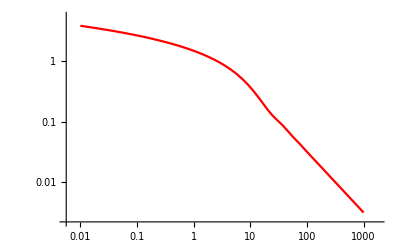

```mathematica
LogLogPlot[{Tpp[t,0.1]},{t,0.01,1000},PlotStyle->{Red}]
```

```mathematica
FullSimplify[Series[Tpp[τ,Λ],{τ,0,1}],Λ>0&&τ>0]
```

1/4 (1-2 EulerGamma+Log[4]-2 Log[Λ τ])+O[τ]^2

```mathematica
FullSimplify[Series[BesselJ[0,x]^2-BesselJ[1,x]^2,{x,Infinity,0}]]
FullSimplify[Series[BesselJ[0,x]^2+BesselJ[1,x]^2,{x,Infinity,0}]]
```

O[1/x]^2+Cos[2 x] (1/(2 π x^2)+O[1/x]^(5/2))+(2/(π x)+O[1/x]^2) Sin[2 x]

Cos[2 x] (-1/(π x^2)+O[1/x]^(5/2))+(2/(π x)+O[1/x]^2)+(1/(8 π x^3)+O[1/x]^(7/2)) Sin[2 x]

```mathematica
PL[τ_,Λ_]=FullSimplify[Tpp[τ,Λ]-Tpm[τ,Λ]]
```

1/24 (-π^2+3 Λ^2 τ^2 HypergeometricPFQ[{1,1,1,3/2},{2,2,2,2,2},-Λ^2 τ^2]-12 (EulerGamma-Log[2])^2-12 Log[Λ]^2-24 Log[Λ] (EulerGamma+Log[τ/2])-12 (2 EulerGamma+Log[τ/4]) Log[τ]+(6 MeijerG[{{1/2},{1}},{{0,0},{-1,0}},Λ^2 τ^2])/(√π))

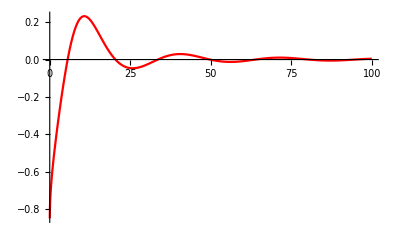

```mathematica
Plot[PL[t,0.1]/Tpm[t,0.1],{t,0.01,100},PlotStyle->{Red},PlotRange->{All,All}]
```

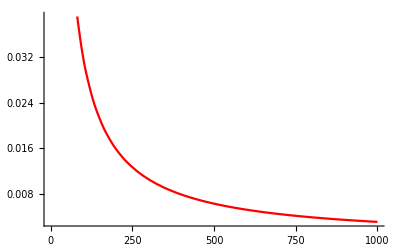

```mathematica
Plot[Tpm[t,0.1],{t,0.01,1000},PlotStyle->{Red}]
```

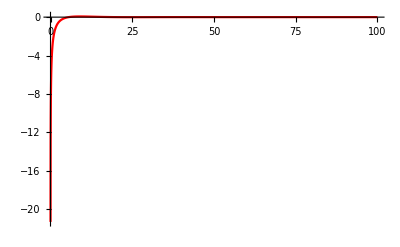

```mathematica
Plot[PL[t,0.1],{t,0.01,100},PlotStyle->{Red},PlotRange->{All,All}]
```

## T^μν: use 1/kp

```mathematica
Exit
```

```mathematica
ηu={0,1,0,0}
```

{0,1,0,0}

```mathematica
guu={{0,1,0,0},{1,0,0,0},{0,0,-1,0},{0,0,0,-1}}
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
Proj[ku_,μ_,ν_]:=guu[[μ,ν]]-(ηu[[μ]] ku[[ν]]+ ηu[[ν]] ku[[μ]])/(ηu.guu.ku)
```

```mathematica
k1:={k1p,k1m,k1x,k1y}
l1:={l1p,l1m,l1x,l1y}
```

```mathematica
δT:=DiagonalMatrix[{0,0,1,1}](*for scalar prodcution of transverse components*)
```

```mathematica
GRuu[ku_,μ_,ν_]:=-I/(ku.guu.ku)Proj[ku,μ,ν]
```

```mathematica
Acl[μ_,ku_,lu_]:=(I/ku[[2]] GRuu[ku,μ,2]+2/((ku-lu).δT.(ku-lu)) 1/(ku.guu.ku)(-(guu.δT.(ku-lu))[[μ]]+ηu[[μ]] ku.δT.(ku-lu)/ku[[1]]))
```

```mathematica
Acl[ku_,lu_]:=Table[Acl[i,ku,lu],{i,1,4}]
```

```mathematica
Acl[k1,l1]
```

{0,-2/(k1p (2 k1m k1p-k1x^2-k1y^2))+(2 (k1x (k1x-l1x)+k1y (k1y-l1y)))/(k1p (2 k1m k1p-k1x^2-k1y^2) ((k1x-l1x)^2+(k1y-l1y)^2)),-k1x/(k1m k1p (2 k1m k1p-k1x^2-k1y^2))+(2 (k1x-l1x))/((2 k1m k1p-k1x^2-k1y^2) ((k1x-l1x)^2+(k1y-l1y)^2)),-k1y/(k1m k1p (2 k1m k1p-k1x^2-k1y^2))+(2 (k1y-l1y))/((2 k1m k1p-k1x^2-k1y^2) ((k1x-l1x)^2+(k1y-l1y)^2))}

```mathematica
DAuu[ku_,μ_,lu_,ν_]:=-I ku[[μ]] Acl[ν,ku,lu]
```

```mathematica
DAuu[ku_,lu_]:=Table[DAuu[ku,μ,lu,ν],{μ,1,4},{ν,1,4}]
```

Therefore, we don' t need this piece, which only gives contributions along the lightcones!

```mathematica
da=-I FullSimplify[ (DAuu[k1,l1]/.{(2 k1m k1p-k1x^2-k1y^2)->1})/(2 (k1p+I ϵ))/.{k1m->  (k1x^2+k1y^2)/(2 (k1p+I ϵ))}]
```

{{0,-((k1x-l1x) l1x+(k1y-l1y) l1y)/(((k1x-l1x)^2+(k1y-l1y)^2) (k1p+ⅈ ϵ)),-(k1p ((2 (k1x-l1x))/((k1x-l1x)^2+(k1y-l1y)^2)-(2 k1x (k1p+ⅈ ϵ))/(k1p (k1x^2+k1y^2))))/(2 (k1p+ⅈ ϵ)),-(k1p ((2 (k1y-l1y))/((k1x-l1x)^2+(k1y-l1y)^2)-(2 k1y (k1p+ⅈ ϵ))/(k1p (k1x^2+k1y^2))))/(2 (k1p+ⅈ ϵ))},{0,-((k1x^2+k1y^2) ((k1x-l1x) l1x+(k1y-l1y) l1y))/(2 k1p ((k1x-l1x)^2+(k1y-l1y)^2) (k1p+ⅈ ϵ)^2),-((k1x^2+k1y^2) ((2 (k1x-l1x))/((k1x-l1x)^2+(k1y-l1y)^2)-(2 k1x (k1p+ⅈ ϵ))/(k1p (k1x^2+k1y^2))))/(4 (k1p+ⅈ ϵ)^2),-((k1x^2+k1y^2) ((2 (k1y-l1y))/((k1x-l1x)^2+(k1y-l1y)^2)-(2 k1y (k1p+ⅈ ϵ))/(k1p (k1x^2+k1y^2))))/(4 (k1p+ⅈ ϵ)^2)},{0,-(k1x ((k1x-l1x) l1x+(k1y-l1y) l1y))/(k1p ((k1x-l1x)^2+(k1y-l1y)^2) (k1p+ⅈ ϵ)),-(k1x ((2 (k1x-l1x))/((k1x-l1x)^2+(k1y-l1y)^2)-(2 k1x (k1p+ⅈ ϵ))/(k1p (k1x^2+k1y^2))))/(2 (k1p+ⅈ ϵ)),-(k1x ((2 (k1y-l1y))/((k1x-l1x)^2+(k1y-l1y)^2)-(2 k1y (k1p+ⅈ ϵ))/(k1p (k1x^2+k1y^2))))/(2 (k1p+ⅈ ϵ))},{0,-(k1y ((k1x-l1x) l1x+(k1y-l1y) l1y))/(k1p ((k1x-l1x)^2+(k1y-l1y)^2) (k1p+ⅈ ϵ)),-(k1y ((2 (k1x-l1x))/((k1x-l1x)^2+(k1y-l1y)^2)-(2 k1x (k1p+ⅈ ϵ))/(k1p (k1x^2+k1y^2))))/(2 (k1p+ⅈ ϵ)),-(k1y ((2 (k1y-l1y))/((k1x-l1x)^2+(k1y-l1y)^2)-(2 k1y (k1p+ⅈ ϵ))/(k1p (k1x^2+k1y^2))))/(2 (k1p+ⅈ ϵ))}}

```mathematica
DA[{k1p_,k1m_,k1x_,k1y_},{l1p_,l1m_,l1x_,l1y_}]=da
```

{{0,-((k1x-l1x) l1x+(k1y-l1y) l1y)/(((k1x-l1x)^2+(k1y-l1y)^2) (k1p+ⅈ ϵ)),-(k1p ((2 (k1x-l1x))/((k1x-l1x)^2+(k1y-l1y)^2)-(2 k1x (k1p+ⅈ ϵ))/(k1p (k1x^2+k1y^2))))/(2 (k1p+ⅈ ϵ)),-(k1p ((2 (k1y-l1y))/((k1x-l1x)^2+(k1y-l1y)^2)-(2 k1y (k1p+ⅈ ϵ))/(k1p (k1x^2+k1y^2))))/(2 (k1p+ⅈ ϵ))},{0,-((k1x^2+k1y^2) ((k1x-l1x) l1x+(k1y-l1y) l1y))/(2 k1p ((k1x-l1x)^2+(k1y-l1y)^2) (k1p+ⅈ ϵ)^2),-((k1x^2+k1y^2) ((2 (k1x-l1x))/((k1x-l1x)^2+(k1y-l1y)^2)-(2 k1x (k1p+ⅈ ϵ))/(k1p (k1x^2+k1y^2))))/(4 (k1p+ⅈ ϵ)^2),-((k1x^2+k1y^2) ((2 (k1y-l1y))/((k1x-l1x)^2+(k1y-l1y)^2)-(2 k1y (k1p+ⅈ ϵ))/(k1p (k1x^2+k1y^2))))/(4 (k1p+ⅈ ϵ)^2)},{0,-(k1x ((k1x-l1x) l1x+(k1y-l1y) l1y))/(k1p ((k1x-l1x)^2+(k1y-l1y)^2) (k1p+ⅈ ϵ)),-(k1x ((2 (k1x-l1x))/((k1x-l1x)^2+(k1y-l1y)^2)-(2 k1x (k1p+ⅈ ϵ))/(k1p (k1x^2+k1y^2))))/(2 (k1p+ⅈ ϵ)),-(k1x ((2 (k1y-l1y))/((k1x-l1x)^2+(k1y-l1y)^2)-(2 k1y (k1p+ⅈ ϵ))/(k1p (k1x^2+k1y^2))))/(2 (k1p+ⅈ ϵ))},{0,-(k1y ((k1x-l1x) l1x+(k1y-l1y) l1y))/(k1p ((k1x-l1x)^2+(k1y-l1y)^2) (k1p+ⅈ ϵ)),-(k1y ((2 (k1x-l1x))/((k1x-l1x)^2+(k1y-l1y)^2)-(2 k1x (k1p+ⅈ ϵ))/(k1p (k1x^2+k1y^2))))/(2 (k1p+ⅈ ϵ)),-(k1y ((2 (k1y-l1y))/((k1x-l1x)^2+(k1y-l1y)^2)-(2 k1y (k1p+ⅈ ϵ))/(k1p (k1x^2+k1y^2))))/(2 (k1p+ⅈ ϵ))}}

```mathematica
k2:={k2p,k2m,k2x,k2y}
l2:={l2p,l2m,l2x,l2y}
```

```mathematica
Fuu[ku_,lu_]:=Module[{dA},
dA=DA[ku,lu];
dA-Transpose[dA]
]
```

```mathematica
Tuu[k1u_,l1u_,k2u_,l2u_]:=Module[{f1uu,f2uu},
f1uu=Fuu[k1u,l1u];f2uu=(Fuu[k2u,l2u]/.{k2u[[3]]->-k1u[[3]],k2u[[4]]->-k1u[[4]],l2u[[3]]->-l1u[[3]],l2u[[4]]->-l1u[[4]]});
f1uu.guu.f2uu+Tr[Transpose[f1uu].guu.f2uu.guu] guu/4
]
```

```mathematica
Tμν=Tuu[k1,l1,k2,l2]/(l1.δT.l1)^2;
```

```mathematica
I0[xm_,xp_,k_]:=- (k xp)/Sqrt[2 xp xm] BesselJ[1,k Sqrt[2 xp xm]]
I1[xm_,xp_,k_]:=-I BesselJ[0,k Sqrt[2 xp xm]]
I2[xm_,xp_,k_]:=-(2 xm)/(k Sqrt[2 xp xm])BesselJ[1,k Sqrt[2 xp xm]]
```

```mathematica
FullSimplify[I D[I2[xm,xp,k],xm]-I1[xm,xp,k]]
FullSimplify[I D[I1[xm,xp,k],xm]-I0[xm,xp,k]]
```

0

0

```mathematica
overall:=-(4 π αs)^3 (CF A1 A2)/(2 S1 S2) 
l1Itg:=l1.δT.l1 (k1-l1).δT.(k1-l1) 2 π Log[k1.δT.k1/Λ^2] /(2π)^4/k1.δT.k1
```

```mathematica
Limit[FullSimplify[(k1p+ⅈ ϵ) (-ⅈ k2p+ϵ) Tμν[[1,1]]],ϵ->0]/((k1p+ⅈ ϵ) (-ⅈ k2p+ϵ))
```

(ⅈ k1p k2p)/((k1x^2+k1y^2) ((k1x-l1x)^2+(k1y-l1y)^2) (l1x^2+l1y^2) (k1p+ⅈ ϵ) (-ⅈ k2p+ϵ))

```mathematica
Expand[FullSimplify[Tμν[[2,2]]]]
```

-(k1x^4 l1x^2)/(4 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(k1x^2 k1y^2 l1x^2)/(2 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(k1y^4 l1x^2)/(4 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(k1x^3 l1x^3)/(2 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(k1x k1y^2 l1x^3)/(2 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(k1x^2 l1x^4)/(4 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(k1y^2 l1x^4)/(4 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(k1x^2 k1y l1x^2 l1y)/(2 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(k1y^3 l1x^2 l1y)/(2 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(k1x^4 l1y^2)/(4 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(k1x^2 k1y^2 l1y^2)/(2 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(k1y^4 l1y^2)/(4 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(k1x^3 l1x l1y^2)/(2 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(k1x k1y^2 l1x l1y^2)/(2 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(k1x^2 l1x^2 l1y^2)/(2 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(k1y^2 l1x^2 l1y^2)/(2 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(k1x^2 k1y l1y^3)/(2 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(k1y^3 l1y^3)/(2 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(k1x^2 l1y^4)/(4 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(k1y^2 l1y^4)/(4 ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1x^5 l1x ϵ)/(4 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1x^3 k1y^2 l1x ϵ)/(2 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1x k1y^4 l1x ϵ)/(4 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1x^5 l1x ϵ)/(4 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1x^3 k1y^2 l1x ϵ)/(2 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1x k1y^4 l1x ϵ)/(4 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1x^4 l1x^2 ϵ)/(4 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1x^2 k1y^2 l1x^2 ϵ)/(2 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1y^4 l1x^2 ϵ)/(4 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1x^4 l1x^2 ϵ)/(4 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1x^2 k1y^2 l1x^2 ϵ)/(2 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1y^4 l1x^2 ϵ)/(4 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1x^3 l1x^3 ϵ)/(4 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1x k1y^2 l1x^3 ϵ)/(4 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1x^3 l1x^3 ϵ)/(4 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1x k1y^2 l1x^3 ϵ)/(4 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1x^2 l1x^4 ϵ)/(4 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1y^2 l1x^4 ϵ)/(4 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1x^2 l1x^4 ϵ)/(4 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1y^2 l1x^4 ϵ)/(4 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1x^4 k1y l1y ϵ)/(4 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1x^2 k1y^3 l1y ϵ)/(2 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1y^5 l1y ϵ)/(4 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1x^4 k1y l1y ϵ)/(4 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1x^2 k1y^3 l1y ϵ)/(2 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1y^5 l1y ϵ)/(4 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1x^2 k1y l1x^2 l1y ϵ)/(4 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1y^3 l1x^2 l1y ϵ)/(4 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1x^2 k1y l1x^2 l1y ϵ)/(4 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1y^3 l1x^2 l1y ϵ)/(4 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1x^4 l1y^2 ϵ)/(4 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1x^2 k1y^2 l1y^2 ϵ)/(2 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1y^4 l1y^2 ϵ)/(4 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1x^4 l1y^2 ϵ)/(4 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1x^2 k1y^2 l1y^2 ϵ)/(2 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1y^4 l1y^2 ϵ)/(4 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1x^3 l1x l1y^2 ϵ)/(4 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1x k1y^2 l1x l1y^2 ϵ)/(4 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1x^3 l1x l1y^2 ϵ)/(4 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1x k1y^2 l1x l1y^2 ϵ)/(4 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1x^2 l1x^2 l1y^2 ϵ)/(2 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1y^2 l1x^2 l1y^2 ϵ)/(2 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1x^2 l1x^2 l1y^2 ϵ)/(2 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1y^2 l1x^2 l1y^2 ϵ)/(2 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1x^2 k1y l1y^3 ϵ)/(4 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1y^3 l1y^3 ϵ)/(4 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1x^2 k1y l1y^3 ϵ)/(4 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(ⅈ k1y^3 l1y^3 ϵ)/(4 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1x^2 l1y^4 ϵ)/(4 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1y^2 l1y^4 ϵ)/(4 k1p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1x^2 l1y^4 ϵ)/(4 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(ⅈ k1y^2 l1y^4 ϵ)/(4 k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(k1x^6 ϵ^2)/(4 k1p k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(3 k1x^4 k1y^2 ϵ^2)/(4 k1p k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(3 k1x^2 k1y^4 ϵ^2)/(4 k1p k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(k1y^6 ϵ^2)/(4 k1p k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(k1x^4 l1x^2 ϵ^2)/(2 k1p k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(k1x^2 k1y^2 l1x^2 ϵ^2)/(k1p k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(k1y^4 l1x^2 ϵ^2)/(2 k1p k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(k1x^2 l1x^4 ϵ^2)/(4 k1p k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(k1y^2 l1x^4 ϵ^2)/(4 k1p k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(k1x^4 l1y^2 ϵ^2)/(2 k1p k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(k1x^2 k1y^2 l1y^2 ϵ^2)/(k1p k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)-(k1y^4 l1y^2 ϵ^2)/(2 k1p k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(k1x^2 l1x^2 l1y^2 ϵ^2)/(2 k1p k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(k1y^2 l1x^2 l1y^2 ϵ^2)/(2 k1p k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(k1x^2 l1y^4 ϵ^2)/(4 k1p k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)+(k1y^2 l1y^4 ϵ^2)/(4 k1p k2p ((k1x-l1x)^2+(k1y-l1y)^2)^2 (l1x^2+l1y^2)^2 (k1p+ⅈ ϵ)^2 (k2p+ⅈ ϵ)^2)

A pain in the ass.

```mathematica
Series[BesselJ[1,x],{x,0,1}]
Series[BesselJ[1,x],{x,Infinity,1}]
Series[BesselJ[0,x],{x,0,1}]
```

x/2+O[x]^2

Cos[π/4+x] (-√(2/π) √(1/x)+O[1/x]^(3/2))+((3 (1/x)^(3/2))/(4 √(2 π))+O[1/x]^2) Sin[π/4+x]

1+O[x]^2

## Transformation

```mathematica
M={{1,1},{1,-1}}/Sqrt[2]
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

```mathematica
M.M
```

{{1,0},{0,1}}

```mathematica
Tuu=FullSimplify[M.{{Tpp,Tpm},{Tmp,Tmm}}.Transpose[M]]
```

{{1/2 (Tmm+Tmp+Tpm+Tpp),1/2 (-Tmm+Tmp-Tpm+Tpp)},{1/2 (-Tmm-Tmp+Tpm+Tpp),1/2 (Tmm-Tmp-Tpm+Tpp)}}

At z = 0,

```mathematica
FullSimplify[Tuu/.{Tmp->Tpm,Tmm->Tpp}]
```

{{Tpm+Tpp,0},{0,-Tpm+Tpp}}

```mathematica
Integrate[Log[x],x]
```

-x+x Log[x]